```mathematica
Quit
```

```mathematica
Dgg=gg'[r]==(2 k gg[r]^3 NN[r]^2-2 k gg[r]^5 NN[r]^2-w^2 η gg[r]^3 ϕ[r]^2+r^2 w^2 α gg[r]^5 ϕ[r]^2+w^2 η gg[r]^5 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2+η gg[r] NN[r]^2 ϕ'[r]^2+r^2 α gg[r]^3 NN[r]^2 ϕ'[r]^2+η gg[r]^3 NN[r]^2 ϕ'[r]^2+4 r η gg[r] NN[r]^2 ϕ'[r] ϕ''[r])/(2 r (2 k gg[r]^2 NN[r]^2-w^2 η gg[r]^2 ϕ[r]^2+3 η NN[r]^2 ϕ'[r]^2));

DNN=NN'[r]==(NN[r] (gg[r]^4 (w^2 (r^2 α+η) ϕ[r]^2+NN[r]^2 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2))-3 η NN[r]^2 ϕ'[r]^2+gg[r]^2 (-w^2 η ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))))/(gg[r]^2 (4 k r NN[r]^2-2 r w^2 η ϕ[r]^2)+6 r η NN[r]^2 ϕ'[r]^2);

DDPhi=ϕ''[r]==(-gg[r]^5 (w^2 (r^2 α+η)-Subscript[λ, 1] m^2 r^2 NN[r]^2) ϕ[r]-3 η NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 η ϕ[r]-NN[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r])+η gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))/(gg[r] NN[r] ((-η+(r^2 α+η) gg[r]^2) NN[r]-2 r η NN'[r]));
```

```mathematica
Seqphi=(ϕ''[r](gg[r] NN[r] ((-η+(r^2 α+η) gg[r]^2) NN[r]-2 r η NN'[r]))-(-gg[r]^5 (w^2 (r^2 α+η)-Subscript[λ, 1] m^2 r^2 NN[r]^2) ϕ[r]-3 η NN[r] gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]+gg[r]^2 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+gg[r]^3 (w^2 η ϕ[r]-NN[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r])+η gg[r] NN[r] ϕ'[r] (3 NN'[r]+2 r NN''[r]))//Simplify)==0;

SeqN=(NN'[r](gg[r]^2 (4 k r NN[r]^2-2 r w^2 η ϕ[r]^2)+6 r η NN[r]^2 ϕ'[r]^2)-(NN[r] (gg[r]^4 (w^2 (r^2 α+η) ϕ[r]^2+NN[r]^2 (2 k-Subscript[λ, 1] m^2 r^2 ϕ[r]^2))-3 η NN[r]^2 ϕ'[r]^2+gg[r]^2 (-w^2 η ϕ[r] (ϕ[r]+4 r ϕ'[r])+NN[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))))//Simplify)==0;

Seqg=(gg'[r](2 r (2 k gg[r]^2 NN[r]^2-w^2 η gg[r]^2 ϕ[r]^2+3 η NN[r]^2 ϕ'[r]^2))-(2 k gg[r]^3 NN[r]^2-2 k gg[r]^5 NN[r]^2-w^2 η gg[r]^3 ϕ[r]^2+r^2 w^2 α gg[r]^5 ϕ[r]^2+w^2 η gg[r]^5 ϕ[r]^2+Subscript[λ, 1] m^2 r^2 gg[r]^5 NN[r]^2 ϕ[r]^2+η gg[r] NN[r]^2 ϕ'[r]^2+r^2 α gg[r]^3 NN[r]^2 ϕ'[r]^2+η gg[r]^3 NN[r]^2 ϕ'[r]^2+4 r η gg[r] NN[r]^2 ϕ'[r] ϕ''[r])//Simplify)==0;
```

## Serie

```mathematica
Sphi=Series[ϕ[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdphi=Series[ ϕ'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SN=Series[NN[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SdN=Series[NN'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sg=Series[gg[r],{r,0,2}]/.φ'[0]-> 0//Simplify
```

φ[0]+1/2 φ''[0] r^2+O[r]^3

φ''[0] r+1/2 φ^(3)[0] r^2+O[r]^3

NN[0]+NN'[0] r+1/2 NN''[0] r^2+O[r]^3

NN'[0]+NN''[0] r+1/2 NN^(3)[0] r^2+O[r]^3

gg[0]+gg'[0] r+1/2 gg''[0] r^2+O[r]^3

```mathematica
SeqN=Series[SeqN,{r, 0,3}]//Simplify;
Seqg=Series[Seqg,{r, 0,3}]//Simplify;
Seqphi=Series[Seqphi,{r, 0,3}]//Simplify;

SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;

ordN0= Coefficient[SeqN1[[1]],r,0]
ordg0= Coefficient[Seqg1[[1]],r,0]
ordphi0=Coefficient[Seqphi1[[1]],r,0]
```

-gg[0]^2 (-1+gg[0]^2) NN[0] (2 k NN[0]^2+w^2 η φ[0]^2)

gg[0]^3 (-1+gg[0]^2) (2 k NN[0]^2-w^2 η φ[0]^2)

η gg[0] (-1+gg[0]^2) (w^2 gg[0]^2 φ[0]+NN[0]^2 φ''[0])

```mathematica
ordN1=Coefficient[SeqN1[[1]],r];
ordg1=Coefficient[Seqg1[[1]],r];
ordphi1=Coefficient[Seqphi1[[1]],r];

ordN2=Coefficient[SeqN1[[1]], r,2];
ordg2=Coefficient[Seqg1[[1]], r,2];
ordphi2=Coefficient[Seqphi1[[1]], r,2];

ordN3=Coefficient[SeqN1[[1]], r,3];
ordg3=Coefficient[Seqg1[[1]], r,3];
ordphi3=Coefficient[Seqphi1[[1]], r,3];
```

```mathematica
gzero=Last[Solve[ordN0==0, gg[0]]//Simplify]
ddphi=Last[Solve[ordphi0==0, Derivative[2][φ][0]]//Simplify]/.gzero[[1]]

(* Order one *)
{dg,dN}=Last@Solve[{ordN1==0,ordg1==0}//.{ddphi[[1]],gzero[[1]]},{gg'[0],NN'[0]}]
dddphi=Last[Solve[ordphi1==0//.ddphi[[1]]//.{dN,dg},Derivative[3][φ][0]]//Simplify]

(* Order two *)
{ddg,ddN}=Last@Solve[{ordN2==0,ordg2==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg},{gg''[0],NN''[0]}]

(* Order 3 *)
{dddg,dddN}=Last@Solve[{ordN3==0,ordg3==0}//.{ddphi[[1]],dddphi[[1]],gzero[[1]],dN,dg,ddg,ddN},{ Derivative[3][gg][0], Derivative[3][NN][0]}]
```

{gg[0]→1}

{φ''[0]→-(w^2 φ[0])/NN[0]^2}

{gg'[0]→0,NN'[0]→0}

{φ^(3)[0]→0}

{gg''[0]→-(-6 w^4 η φ[0]^2-w^2 α NN[0]^2 φ[0]^2-L1 mS^2 NN[0]^4 φ[0]^2)/(3 NN[0]^2 (2 k NN[0]^2-w^2 η φ[0]^2)),NN''[0]→-(NN[0] (-12 k w^4 η φ[0]^2-4 k w^2 α NN[0]^2 φ[0]^2+2 k L1 mS^2 NN[0]^4 φ[0]^2+w^4 α η φ[0]^4-2 L1 mS^2 w^2 η NN[0]^2 φ[0]^4))/(3 (2 k NN[0]^2-w^2 η φ[0]^2)^2)}

{gg^(3)[0]→0,NN^(3)[0]→0}

Algoritmo

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==1,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];*)

AppendTo[SeidelBCList,{NN[rMin]==SN/.{dN,ddN,dddN}, gg[rMin] == Sg/.{gzero[[1]],dg,ddg,dddg}, φ[rMin] == Sphi/.{ddphi[[1]],dddphi[[1]]},NN'[rMin]==SdN/.{dN,ddN,dddN},φ'[rMin] ==Sdphi/.{ddphi[[1]],dddphi[[1]]}}/.{NN[0]-> 1,φ[0]-> ϕ0,r-> rMin}//Normal];
```

```mathematica
SeidelBCList
```

{{NN[rMin]==1-(rMin^2 (2 k L1 mS^2 ϕ0^2-4 k w^2 α ϕ0^2-12 k w^4 η ϕ0^2-2 L1 mS^2 w^2 η ϕ0^4+w^4 α η ϕ0^4))/(6 (2 k-w^2 η ϕ0^2)^2),gg[rMin]==1-(rMin^2 (-L1 mS^2 ϕ0^2-w^2 α ϕ0^2-6 w^4 η ϕ0^2))/(6 (2 k-w^2 η ϕ0^2)),φ[rMin]==ϕ0-1/2 rMin^2 w^2 ϕ0,NN'[rMin]==-(rMin (2 k L1 mS^2 ϕ0^2-4 k w^2 α ϕ0^2-12 k w^4 η ϕ0^2-2 L1 mS^2 w^2 η ϕ0^4+w^4 α η ϕ0^4))/(3 (2 k-w^2 η ϕ0^2)^2),φ'[rMin]==-rMin w^2 ϕ0}}

```mathematica
(* 
Eta0={{0.01, 0.9666934756769426, 30},{0.015, 0.9513028191707326, 30},{0.02,0.936499160324931,30},{0.03,0.9089249484829031,30},{0.04,0.8839540649030964,30},{0.042, 0.8792629731066374,30},{0.044, 0.8746722299517371,30},{0.046,0.8701790720379096,30},{0.048,0.8657853050155142,30},{0.05,0.8614888676987846,30}};

Etam03={{0.015, 0.9500845521966582,30},{0.02,0.9343424742221126,30},{0.03,0.9040820993159883,30},{0.04,0.8752978332207497,30},{0.042,0.8697014596725171,25},{0.044,0.8641542359799456,30},{0.046,0.8586551380932376,30},{0.048,0.8532017468841957,30},{0.05,0.8477932073572596,30}};
*)
```

## G_eff

```mathematica
BS={0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032736825266425024546711200243289808219829642490431642279`30.,200.07000000000227,30,0,0.01`30.};
```

```mathematica
Bs={0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032730022983853821303561268400154449192330540462007821894`30.,176,30,-0.3,0.01`30.};
```

```mathematica
Bs={0.010399999999999999522604099411182687617838382720947265625`30.,1.0357611351366596528899535652699588110204099697561632096197`30.,60.070000000000086,30,-0.3,0.01`30.};
```

```mathematica
Bs={0.0350000000000000033306690738754696212708950042724609375`30.,1.1373429787846627692076372825875755796093402594237886660267`30.,30.070000000000014,30,-0.3,0.01`30.};
```

```mathematica
Bs={0.07,1.525012688428300000,12,30,-2,10^-3};
```

```mathematica
Bs={0.0200000000000000004163336342344337026588618755340576171875`30.,1.07214820500709030064187941296212677927572584553379900379`30.,35.06100000000003,30,-2,0.001`30.};
```

```mathematica
Bs={0.0010000000000000000208166817117216851329430937767028808594`30.,1.0032686979500788585962945356690317996683162583659206628079`30.,176.06099999999995,30,-2,0.001`30.};
```

```mathematica
Bs={0.070000000000000006661338147750939242541790008544921875`30.,1.3339336275418824559937050199198665006870666414577333999835`30.,20.070000000000043,30,-0.3,0.01`30.};
```

```mathematica
Bs={0.07,1.350463702269447,30.,30.,0.,1.*^-8};
```

```mathematica
Bs={0.03013333333333333141634824414722970686852931976318359375`30.,1.116621675308330270834470692444677922878711745038039017396`30.,40.06999999999989,30,0,0.01`30.};
```

```mathematica
Bs={0.05,1.219018571342151,20.,30.,0.,1.*^-8}
```

{0.05,1.21902,20.,30.,0.,1.×10^-8}

0.964954

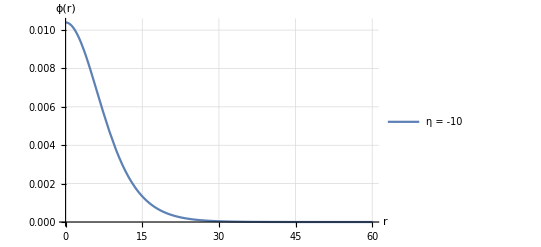

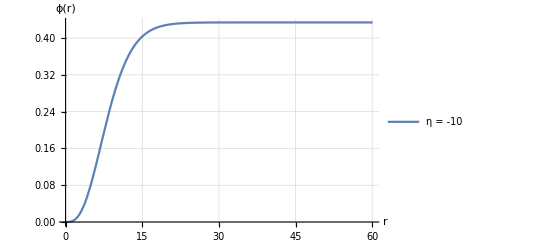

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}, MaxSteps->10^6];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

M[r_]:=1/2 r (1-1/gg[r]^2);

Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M95=0.95Evaluate[M[rMax]/.s][[1]]; (* masa física *)
MM[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s];
rad=Last[FindRoot[MM[r]==M95,{r,rMin+0.5,rMax}]];
Print[rad];
Print["masa95 = ", M95];
```

r→20.3922

masa95 = 0.429578

```mathematica
0.6287138717681229*8π
```

15.8013

```mathematica
data={};
AppendTo[data,{"r","phi","M"}];
(*rmax=None*)
Do[
AppendTo[data,{r,Last@Evaluate[φ[r]/.s]*√(8.π),Last@Evaluate[M[r]/.s]8.π}],
{r,rMin,rMax+0.05,0.05}
]
```

```mathematica
data
```

```mathematica
Export["BS_sig_025.dat",data]
```

BS_sig_025.dat

```mathematica
datos={};
Do[AppendTo[datos,{r,(Evaluate[φ[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]

datos2={};
Do[AppendTo[datos2,{r,(Evaluate[M[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]
```

```mathematica
Export["HXm2A0001.dat",datos]
(*Export["HX_Mm03A035.dat",datos2]*)
```

HXm2A0001.dat

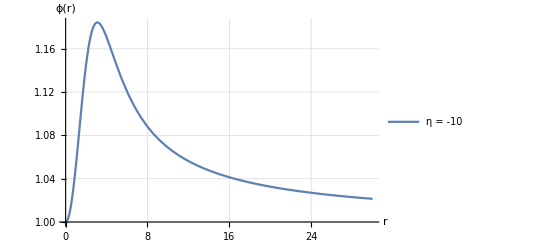

```mathematica
Plot[{Evaluate[gg[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
datos3={};
Do[AppendTo[datos3,{r,(Evaluate[gg[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]
```

```mathematica
Export["BHXgm109.dat",datos3]
```

KGg.dat

```mathematica
(* sin el reescalamiento *)
```

1.4936

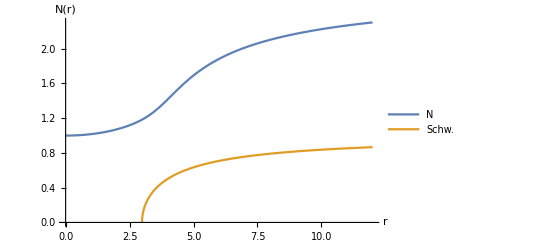

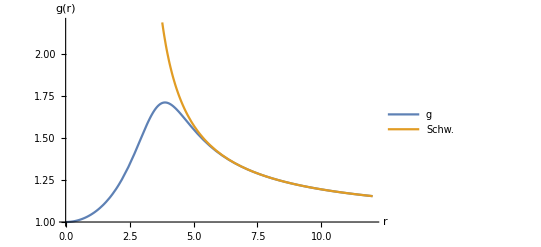

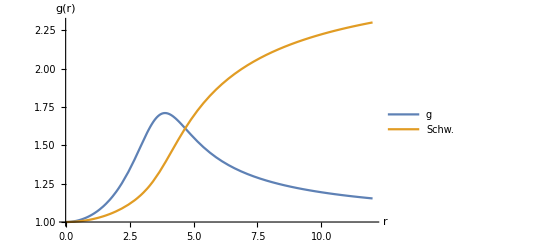

```mathematica
Masa=MM[rMax][[1]]
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},{r,rMin,rMax},Background->White,PlotLegends->Placed[{"N ","Schw."},{0.85,0.56}],AxesLabel->{"r","N(r)"},AxesOrigin->{0,0},PlotRange->All]

Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g ","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g ","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
(* Reescalando *)
```

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];
```

```mathematica
w2
```

0.99654

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

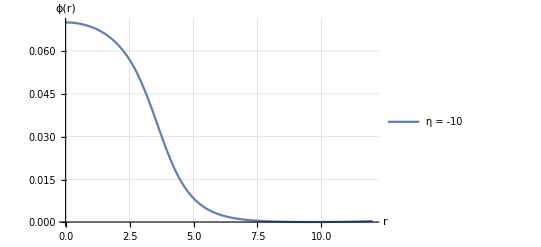

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w= w2(*w2*);(*0.8967355292683497*)
rMax=SetPrecision[Bs[[3]],prec](*28*);
rMin=SetPrecision[Bs[[6]],prec]; (*10^-6*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

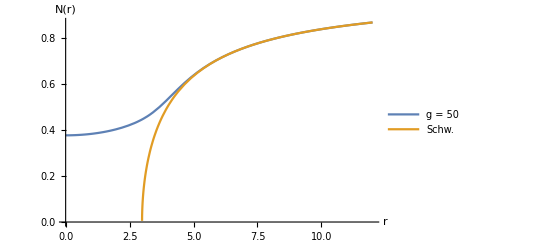

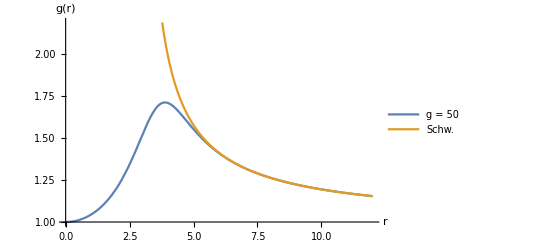

```mathematica
(* comprobando que se pega a Schw *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
datos3={};
Do[AppendTo[datos3,{r,(Evaluate[NN[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]
```

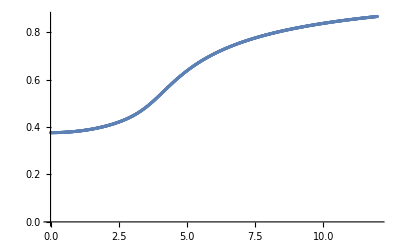

```mathematica
ListPlot[datos3]
```

```mathematica
Export["HXNm2A007.dat",datos3]
```

HXNm2A007.dat

Definiendo  G_eff/G-1

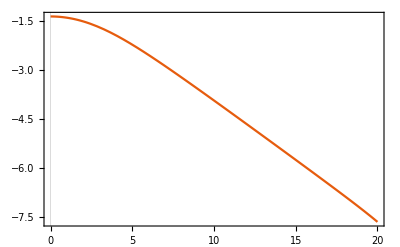

```mathematica
Van[r_]:=Abs[(gg[r]^2 NN[r]^2)/(gg[r]^2 NN[r]^2+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2))-1];(*|Subscript[G, N]/G-1|*)

B=Plot[Evaluate[Log10@Van[r]/.s],{r,rMin,rMax(*rMax*)}, PlotRange->All,AxesOrigin->{0,0},PlotTheme->"Scientific"](*para rho=0.03, el radio máximo es 15 *)
```

```mathematica
FindRoot[Evaluate[Log10@Van[r]/.s][[1]]==Log10[0.000022],{r,10}]
```

{r→13.5325}

```mathematica
(*-(w^2 ϕ[r]^2)/NN[r]^2+ϕ'[r]^2/gg[r]^2*)
```

```mathematica
funcX[r_]:=(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)/(gg[r]^2 NN[r]^2)
```

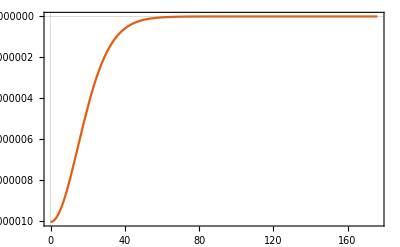

```mathematica
x=Plot[Evaluate[funcX[r]/.s],{r,rMin,rMax(*rMax*)}, PlotRange->All,AxesOrigin->{0,0},PlotTheme->"Scientific"]
```

```mathematica
Evaluate[funcX[r]/.s]/.r->rMin
```

{-0.0015846}

```mathematica
datos={};
Do[AppendTo[datos,{r,(Evaluate[funcX[rm]/.s]/.rm-> r)[[1]]}],{r,rMin,rMax,0.01}]
```

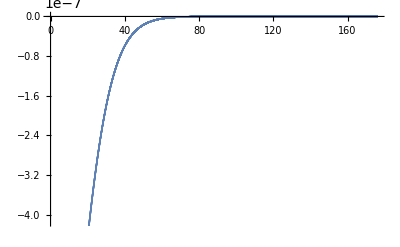

```mathematica
ListPlot@datos
```

```mathematica
Export["HX_m2A0001.dat",datos]
```

HX_m2A0001.dat

```mathematica
a=Import["HX_m2A007.dat"];
b=Import["HX_m03A007.dat"];
c=Import["BSA007.dat"];
```

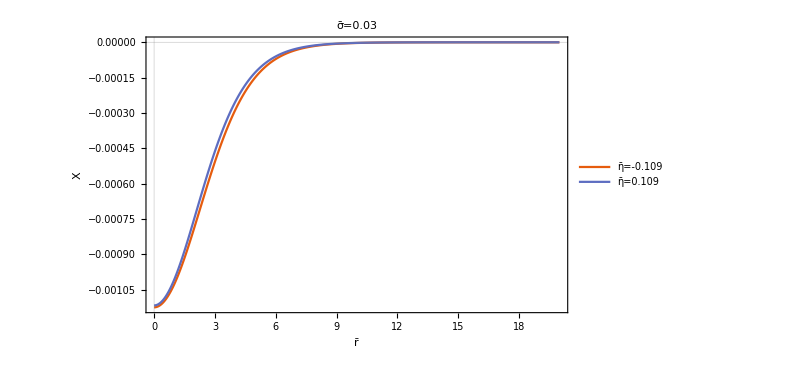

```mathematica
ListPlot[{c,b, a},AxesOrigin->{0,0},PlotTheme->"Scientific", Joined->True,FrameLabel->{"r̄","X"},PlotLegends->Placed[{"η̄=-0.109", "η̄=0.109"},{0.75,0.75}],PlotLabel->"σ̄=0.03", PlotRange->{{0,20},All},ImageSize->600,BaseStyle->14]
```

```mathematica
ListPlot[{a,b},AxesOrigin->{0,0},PlotTheme->"Scientific", Joined->True,FrameLabel->{"r̄","X"},PlotLegends->Placed[{"(ϕ̄)_0=0.03", "(ϕ̄)_0 = 0.015"},{0.75,0.75}],PlotLabel->"η̄=-0.3", PlotRange->{{0,20},All},ImageSize->600,BaseStyle->14]
```

```mathematica
boxphi[r_]:=(ⅇ^(ⅈ w t) (r w^2 gg[r]^3 ϕ[r]-r NN[r]^2 gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r]))))/(r gg[r]^3 NN[r]^2)ⅇ^(-ⅈ w t)//Simplify
```

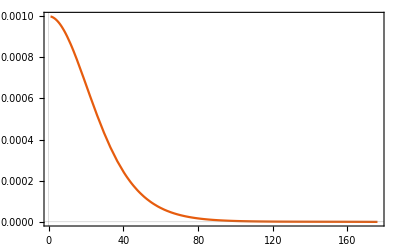

```mathematica
Plot[Evaluate[boxphi[r]/.s],{r,1,rMax}, PlotRange->All,AxesOrigin->{0,0},PlotTheme->"Scientific"]
```

```mathematica
Evaluate[boxphi[r]/.s]/.r-> rMax
```

{0.000239867+0. ⅈ}

```mathematica
datos={};
Do[AppendTo[datos,{r,(Evaluate[boxphi[rm]/.s]/.rm-> r)[[1]]}],{r,1,rMax,0.01}]
```

```mathematica
box=Interpolation[datos,InterpolationOrder->1,Method->"Spline"]
```

InterpolatingFunction[…]

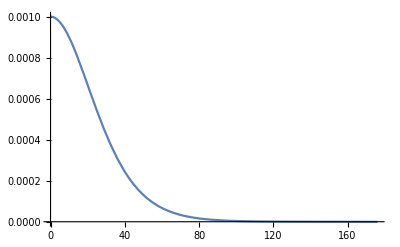

```mathematica
Plot[box[r],{r,0.001,rMax}]
```

```mathematica
datos2={};
Do[AppendTo[datos2,{r,box[r]}],{r,0.001,rMax,0.01}]
```

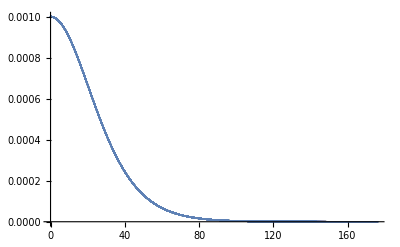

```mathematica
Show[{ListPlot@datos2,ListPlot@datos}]
```

```mathematica
["HX_m03A007.dat"];"BSA007.dat"
```

```mathematica
Export["HBoxX_m2A0001.dat",datos2]
```

HBoxX_m2A0001.dat

Mostrando el punto r_95 y el límite

```mathematica
radLim=Last@FindRoot[Evaluate[Log10@Van[r]/.s][[1]]==-4.327902142064283,{r,10}] (* calculando el radio límite *)
```

r→12.5555

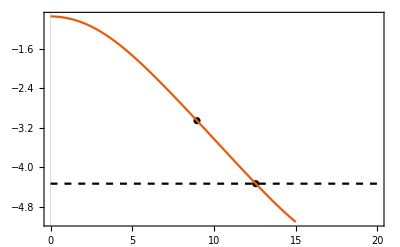

```mathematica
A=ListPlot[{{rad[[2]],Log10@ (Evaluate[Van[r]/.s]/.r-> rad[[2]])[[1]]},{radLim[[2]],Log10@( Evaluate[Van[r]/.s]/.r-> radLim[[2]])[[1]]}},PlotTheme->"Scientific",PlotStyle->{Red,Black}];

c=Plot[y=-4.327902142064283,{x,rMin,(*15*) rMax},PlotStyle-> {{Dashed,Black}}];

Show[{A,B,c},PlotRange-> {{0,(*15*) rMax},Automatic},AxesOrigin-> {0,0}]
```